{{iu[t]→InterpolatingFunction[…][t],ic1[t]→InterpolatingFunction[…][t],ir1[t]→InterpolatingFunction[…][t],u1[t]→InterpolatingFunction[…][t],u2[t]→InterpolatingFunction[…][t]}}

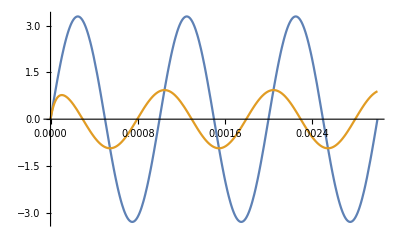

```mathematica
ClearAll["Global`*"]
rov={
0==iu[t]+ic1[t],
ic1[t]==ir1[t],
uz[t]==u1[t],
ic1[t]==c1*(u1'[t]-u2'[t]),
u2[t]==r1*ir1[t],
u1[0]==0,
u2[0]==0
};
sou={
r1->47000,
c1->10^-9,
uz[t]->3.3*Sin[2π*f*t],
f->1000
};
dos=rov//.sou;
reseni = NDSolve[dos,{iu[t],ic1[t],ir1[t],u1[t],u2[t]},{t,0,3/f/.sou},StartingStepSize->10^-9,Method->{"IndexReduction"->Automatic}]
Plot[{u1[t]/.reseni[[1]], u2[t]/.reseni[[1]]},{t,0,3*1/(f/.sou)}]
```